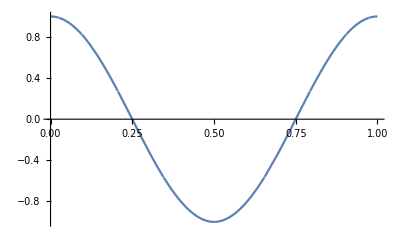

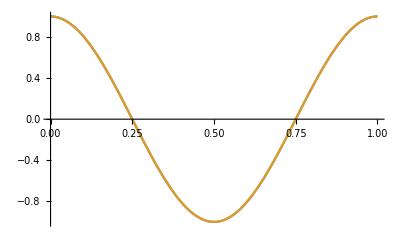

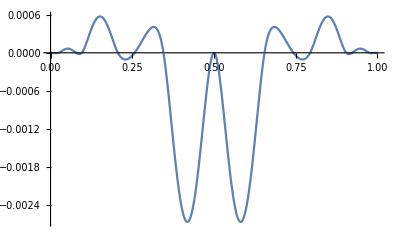

```mathematica
clearAll[delta];
n=12;
(* Изчисляваме възлите: *)
Do[x[k]=Sin[k * Pi/(2*n)]^2, {k,0,n}];
(*x[0]=0, x[n]=1 *)

(* Изчисляваме разстоянията между възлите: Δk = xk+1 - xk *)
Do[delta[k]=x[k+1] - x[k],{k,0,n-1}];

(* Функцията,която ще интерполираме чрез кубичния сплайн s(t): *)
f[t_]:=Cos[2*Pi*t];
(* Разделени разлики divDiff[i]=f[xi,xi+1] *)
Do[divDiff[k]=(f[x[k+1]]-f[x[k]])/delta[k],{k,0,n-1}];

(* Да построим s означава да намерим полиномите от трета степен {Pi(t)}, които представят s(t) в интервалите (xi,xi+1), i=0,...,n-1, съответно. Интерполационните условия на Ермит
                                           Pi(xi)=f(xi)  Pi(xi+1)=f(xi+1)   i=0,...,n-1
                                          P'i(xi)=di    P'i(xi+1)=di+1      i=0,...,n-1
гарантират, че s(t) и s'(t) са непрекъснати в [0,1] и ни позволяват да определим Pi(t) чрез формулата на Нютон:
  Pi(t)=Pi(xi)+Pi[xi,xi]*(t-xi)+Pi[xi,xi,xi+1]*(t-xi)^2+Pi[xi,xi,xi+1,xi+1]*(t-xi)^2*(t-xi+1).
  Pi(xi)=f(xi)
   Pi[xi,xi]=di
  Pi[xi,xi+1]=f[xi,xi+1]
 Pi[xi,xi,xi+1]=(f[xi,xi+1]-di)/Δi
Pi[xi,xi,xi+1,xi+1]=(di+1 - 2*f[xi,xi+1] + di)/(Δi)^2
Остава само да гарантираме s(t) да има непрекъсната втора производна s"(t), т.е. да бъде кубична сплайн-функция. Това е еквивалентно на условията
                                             P"i-1(xi)=P"i(xi)      i=1,...,n-1, които представляват равенства от вида:
                                 Δi*di-1 + 2*(Δi-1 + Δi)*di + Δi-1 * di+1=bi  ,  i=1,...,n-1,
         където                  bi=3*(f[xi-1,xi]*Δi + f[xi,xi+1]*Δi-1),         i=1,...,n-1
   Тоест, ако d0 и dn са избрани по някакъв начин, получаваме система от n-1 уравнения с n-1 неизвестни за определянето на d1,...,dn-1. Тази система е с тридиагонална матрица с доминиращ главен диагонал и ще намерим решението по метода на прогонката. *)

(* Намиране на коефициентите в матрицата: *)
Do[m[i]=delta[i],{i,1,n-1}];
Do[p[i]=2*(delta[i-1]+delta[i]),{i,1,n-1}];
Do[q[i]=delta[i-1],{i,1,n-1}];

(* Намиране на десните страни bi *)
Do[b[i]=3*(divDiff[i-1]*delta[i] + divDiff[i]*delta[i-1]),{i,1,n-1}];
(* Избор на d0 и dn, ще правим пълна кубична сплайнова интерполация: *)
d[0]=f'[x[0]];
d[n]=f'[x[n]];
(* Единствено b1 и bn-1 се различават от общата схема на десните страни: *)
b[1]=b[1]-m[1]*d[0];
b[n-1]=b[n-1]-q[n-1]*d[n];

(* Дотук имаме:      p1*d1 + q1*d2                          =b1
                 m2*d1 + p2*d2 + q2*d3                  =b2
                        m3*d2 + p3*d3 + q3*d4          =b3
                                   ....
                           mn-1 * dn-2 + pn-1 * dn-1 =bn-1
           
*)
(* Прав ход на прогонката: *)
alpha[1]=-q[1]/p[1];
betha[1]=b[1]/p[1];

Do[alpha[k]=(-q[k])/(m[k]*alpha[k-1]+p[k]),{k,2,n-2}];
Do[betha[k]=(b[k]-m[k]*betha[k-1])/(m[k]*alpha[k-1]+p[k]),{k,2,n-1}];

(* Накрая на правея ход намираме dn-1 чрез заместване в последното уравнение и получаваме: *)
d[n-1]=betha[n-1];

(* Обратен ход на прогонката: *)
Do[d[k]=alpha[k]*d[k+1] + betha[k], {k,n-2,1,-1}];
(* След като вече имаме решенията, можем да съставим полиномите Pi(t) по формулата на Нютон от по-горе: *)
P[i_,t_]:=f[x[i]]+d[i]*(t-x[i])+((divDiff[i]-d[i])/delta[i])*(t-x[i])^2 +((d[i+1]-2*divDiff[i]+d[i])/(delta[i])^2)*(t-x[i+1])*(t-x[i])^2 ;

(* Сплайн функция: *)
S[t_]:=Sum[If[t≥x[i]&& t≤x[i+1],P[i,t],0],{i,0,n-1}];

(* Визуализиране на функциите: *)
Plot[S[t],{t,0,1},PlotRange->All]
Plot[{f[t],S[t]},{t,0,1},PlotRange->All]
Plot[{f[t]- S[t]},{t,0,1}]
```